## To mention: -- conjugate-even vectors -- the Rojo, Sato: Existence and construction of nonnegative matrices with complex spectrum (2002) arcticle -- Perron root -- Guo’s theorem

```mathematica
With[{θ=1},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Simplify[ ν A],{m,4,8,2}]]
```

{(0 | ν/2 | 0 | -ν/2
-ν/2 | 0 | ν/2 | 0
0 | -ν/2 | 0 | ν/2
ν/2 | 0 | -ν/2 | 0),(0 | ν/2 | 0 | 0 | 0 | -ν/2
-ν/2 | 0 | ν/2 | 0 | 0 | 0
0 | -ν/2 | 0 | ν/2 | 0 | 0
0 | 0 | -ν/2 | 0 | ν/2 | 0
0 | 0 | 0 | -ν/2 | 0 | ν/2
ν/2 | 0 | 0 | 0 | -ν/2 | 0),(0 | ν/2 | 0 | 0 | 0 | 0 | 0 | -ν/2
-ν/2 | 0 | ν/2 | 0 | 0 | 0 | 0 | 0
0 | -ν/2 | 0 | ν/2 | 0 | 0 | 0 | 0
0 | 0 | -ν/2 | 0 | ν/2 | 0 | 0 | 0
0 | 0 | 0 | -ν/2 | 0 | ν/2 | 0 | 0
0 | 0 | 0 | 0 | -ν/2 | 0 | ν/2 | 0
0 | 0 | 0 | 0 | 0 | -ν/2 | 0 | ν/2
ν/2 | 0 | 0 | 0 | 0 | 0 | -ν/2 | 0)}

```mathematica
Eigenvalues[({{0, ν/2, 0, -ν/2}, {-ν/2, 0, ν/2, 0}, {0, -ν/2, 0, ν/2}, {ν/2, 0, -ν/2, 0}})]//Simplify
```

{ⅈ ν,-ⅈ ν,0,0}

```mathematica
1/(1-Eigenvalues[({{0, ν/2, 0, -ν/2}, {-ν/2, 0, ν/2, 0}, {0, -ν/2, 0, ν/2}, {ν/2, 0, -ν/2, 0}})])//ComplexExpand
```

{1/(1+ν^2)+(ⅈ ν)/(1+ν^2),1/(1+ν^2)-(ⅈ ν)/(1+ν^2),1,1}

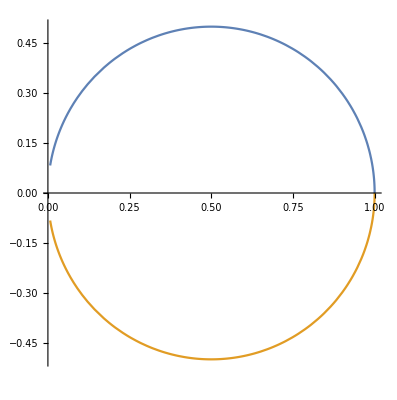

```mathematica
ParametricPlot[{{1/(1+ν^2),ν/(1+ν^2)},{1/(1+ν^2),(- ν)/(1+ν^2)}},{ν,0,12},PlotRange->All]
```

```mathematica
({1/(1+ν^2),ν/(1+ν^2)}-{1/2,0})^2//Total//Simplify
```

1/4

```mathematica
{1/(1+ν^2),ν/(1+ν^2)}^2//Total//Simplify
```

1/(1+ν^2)

```mathematica
({1/(1+ν^2),ν/(1+ν^2)}//Norm)/.Abs->Identity//Simplify
```

√(1/(1+ν^2))

```mathematica
With[{θ=1},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,5,7,2}]]
```

{((16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)
(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)
(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)
(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)
(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4)),((64+80 ν^2+24 ν^4+ν^6)/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (32+32 ν^2+6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2-2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (8+4 ν+4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (-8+4 ν-4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2+2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (-32-32 ν^2-6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6)
(ν (-32-32 ν^2-6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (64+80 ν^2+24 ν^4+ν^6)/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (32+32 ν^2+6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2-2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (8+4 ν+4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (-8+4 ν-4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2+2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6)
(ν^2 (16+12 ν^2+2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (-32-32 ν^2-6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (64+80 ν^2+24 ν^4+ν^6)/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (32+32 ν^2+6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2-2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (8+4 ν+4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (-8+4 ν-4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6)
(ν^3 (-8+4 ν-4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2+2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (-32-32 ν^2-6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (64+80 ν^2+24 ν^4+ν^6)/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (32+32 ν^2+6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2-2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (8+4 ν+4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6)
(ν^3 (8+4 ν+4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (-8+4 ν-4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2+2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (-32-32 ν^2-6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (64+80 ν^2+24 ν^4+ν^6)/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (32+32 ν^2+6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2-2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6)
(ν^2 (16+12 ν^2-2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (8+4 ν+4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (-8+4 ν-4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2+2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (-32-32 ν^2-6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (64+80 ν^2+24 ν^4+ν^6)/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (32+32 ν^2+6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6)
(ν (32+32 ν^2+6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2-2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (8+4 ν+4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^3 (-8+4 ν-4 ν^2+ν^3))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν^2 (16+12 ν^2+2 ν^3+ν^4))/(64+112 ν^2+56 ν^4+7 ν^6) | (ν (-32-32 ν^2-6 ν^4+ν^5))/(64+112 ν^2+56 ν^4+7 ν^6) | (64+80 ν^2+24 ν^4+ν^6)/(64+112 ν^2+56 ν^4+7 ν^6))}

### Nonnegative matrices in the Mathematical Sciences, Chapter 4, Inverse eigenvalue problems, trace inequalities

### For m=4, θ=1, and the 2-power sum, we get the following simple lower bound:

```mathematica
Eigenvalues[({{(2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2))}, {-ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2)}, {ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2)}, {ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2)}})]//ComplexExpand
```

```mathematica
{1/(1+ν^2)+(ⅈ ν)/(1+ν^2),1/(1+ν^2)-(ⅈ ν)/(1+ν^2),1,1}^k//Total//Simplify
```

2+(-ⅈ/(-ⅈ+ν))^k+(ⅈ/(ⅈ+ν))^k

```mathematica
4((2+ν^2)/(2+2 ν^2))^k//Simplify
```

4 ((2+ν^2)/(2+2 ν^2))^k

```mathematica
Table[Reduce[ComplexExpand[2+(-ⅈ/(-ⅈ+ν))^k+(ⅈ/(ⅈ+ν))^k]≥4 ((2+ν^2)/(2+2 ν^2))^k&&ν>0],{k,1,15}]//N
```

{ν>0.,ν≥1.41421,ν≥1.11179,ν≥0.916745,ν≥0.780675,ν≥0.680434,ν≥0.603533,ν≥0.542658,ν≥0.49325,ν≥0.452328,ν≥0.41786,ν≥0.388416,ν≥0.362962,ν≥0.340729,ν≥0.321135}

```mathematica
{ν>0,ν≥√2,ν≥Root[-4+2 #1^2+#1^4&,2],ν≥Root[-48+32 #1^2+24 #1^4+7 #1^6&,2],ν≥Root[-32+32 #1^2+24 #1^4+14 #1^6+3 #1^8&,2]}//N
```

{ν>0.,ν≥1.41421,ν≥1.11179,ν≥0.916745,ν≥0.780675}

### The Hölder-type inequality (with size=4, M=2, K=2 in the book): s_K^M≤ 4^(M-1) s_(K M)

```mathematica
ComplexExpand[{1/(1+ν^2)+(ⅈ ν)/(1+ν^2),1/(1+ν^2)-(ⅈ ν)/(1+ν^2),1,1}^2//Total]^2≤4ComplexExpand[{1/(1+ν^2)+(ⅈ ν)/(1+ν^2),1/(1+ν^2)-(ⅈ ν)/(1+ν^2),1,1}^4//Total]
```

(2+2/((1+ν^2)^2)-(2 ν^2)/((1+ν^2)^2))^2≤4 (2+2/((1+ν^2)^4)-(12 ν^2)/((1+ν^2)^4)+(2 ν^4)/((1+ν^2)^4))

```mathematica
Reduce[(2+2/((1+ν^2)^2)-(2 ν^2)/((1+ν^2)^2))^2≤4 (2+2/((1+ν^2)^4)-(12 ν^2)/((1+ν^2)^4)+(2 ν^4)/((1+ν^2)^4))]//N
```

ν≤-0.782872||ν==0.||ν≥0.782872

With various values of K and M we get various lower bounds:

```mathematica
Reduce[With[{K=2,M=2},ComplexExpand[{1/(1+ν^2)+(ⅈ ν)/(1+ν^2),1/(1+ν^2)-(ⅈ ν)/(1+ν^2),1,1}^K//Total]^M≤4^(M-1)ComplexExpand[{1/(1+ν^2)+(ⅈ ν)/(1+ν^2),1/(1+ν^2)-(ⅈ ν)/(1+ν^2),1,1}^(K M)//Total]]&&ν>0]//N
```

ν≥0.782872

### For m=3, and the 2-power sum, we already get the exact condition for non-negativity:

```mathematica
With[{θ=1},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,3,3,2}]]
```

{((4+ν^2)/(4+3 ν^2) | (ν (2+ν))/(4+3 ν^2) | ((-2+ν) ν)/(4+3 ν^2)
((-2+ν) ν)/(4+3 ν^2) | (4+ν^2)/(4+3 ν^2) | (ν (2+ν))/(4+3 ν^2)
(ν (2+ν))/(4+3 ν^2) | ((-2+ν) ν)/(4+3 ν^2) | (4+ν^2)/(4+3 ν^2))}

```mathematica
Table[Reduce[ComplexExpand@Total[Eigenvalues[({{(4+ν^2)/(4+3 ν^2), (ν (2+ν))/(4+3 ν^2), ((-2+ν) ν)/(4+3 ν^2)}, {((-2+ν) ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (ν (2+ν))/(4+3 ν^2)}, {(ν (2+ν))/(4+3 ν^2), ((-2+ν) ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2)}})]^k]≥3((4+ν^2)/(4+3 ν^2))^k&&ν>0],{k,2,10}]//N
```

{ν≥2.,ν≥1.50828,ν≥1.20518,ν≥1.00261,ν≥0.858749,ν≥0.751652,ν≥0.668912,ν≥0.603074,ν≥0.54942}

### For m=5, and the 2-power sum, we get the lower bound ν ≥ 3.00744 for non-negativity (the exact bound is ν≥4.41114): (for 3-power sums, the lower bound seems to get weaker)

```mathematica
With[{θ=1},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,5,5,2}]]
```

{((16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)
(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)
(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)
(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4) | (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)
(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4) | (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4) | (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4))}

```mathematica
Eigenvalues[({{(16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4)}})]^2
```

{1,1/((16+20 ν^2+5 ν^4)^2)Root[65536+245760 ν^2+368640 ν^4+281600 ν^6+115200 ν^8+24000 ν^10+2000 ν^12+(-16384-40960 ν^2-35840 ν^4-12800 ν^6-1600 ν^8) #1+(1536+2240 ν^2+880 ν^4+100 ν^6) #1^2+(-64-40 ν^2) #1^3+#1^4&,1]^2,1/((16+20 ν^2+5 ν^4)^2)Root[65536+245760 ν^2+368640 ν^4+281600 ν^6+115200 ν^8+24000 ν^10+2000 ν^12+(-16384-40960 ν^2-35840 ν^4-12800 ν^6-1600 ν^8) #1+(1536+2240 ν^2+880 ν^4+100 ν^6) #1^2+(-64-40 ν^2) #1^3+#1^4&,2]^2,1/((16+20 ν^2+5 ν^4)^2)Root[65536+245760 ν^2+368640 ν^4+281600 ν^6+115200 ν^8+24000 ν^10+2000 ν^12+(-16384-40960 ν^2-35840 ν^4-12800 ν^6-1600 ν^8) #1+(1536+2240 ν^2+880 ν^4+100 ν^6) #1^2+(-64-40 ν^2) #1^3+#1^4&,3]^2,1/((16+20 ν^2+5 ν^4)^2)Root[65536+245760 ν^2+368640 ν^4+281600 ν^6+115200 ν^8+24000 ν^10+2000 ν^12+(-16384-40960 ν^2-35840 ν^4-12800 ν^6-1600 ν^8) #1+(1536+2240 ν^2+880 ν^4+100 ν^6) #1^2+(-64-40 ν^2) #1^3+#1^4&,4]^2}

```mathematica
Total@(Eigenvalues[({{(16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4)}})]^2)
```

```mathematica
Reduce[4-2 ν+ν^2≥0&&-8-4 ν^2+ν^3≥0]
```

```mathematica
ν≥Root[-8-4 #1^2+#1^3&,1]//N
```

ν≥4.41114

```mathematica
Total[(ToRadicals@Eigenvalues[({{(16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4)}})])^2]
```

1+((16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))^2)/((16+20 ν^2+5 ν^4)^2)+((16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))^2)/((16+20 ν^2+5 ν^4)^2)+((16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))^2)/((16+20 ν^2+5 ν^4)^2)+((16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))^2)/((16+20 ν^2+5 ν^4)^2)

```mathematica
Reduce[Total[(ToRadicals@Eigenvalues[({{(16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4)}})])^2]≥5((16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4))^2&&ν>0]
```

ν≥Root[-32-24 #1^2-6 #1^4+#1^6&,2]

```mathematica
ν≥Root[-256-320 #1^2-160 #1^4-20 #1^6+11 #1^8+#1^10&,2]//N
```

ν≥2.14978

```mathematica
ν≥Root[-32-24 #1^2-6 #1^4+#1^6&,2]//N
```

ν≥3.00744

```mathematica
ν≥Root[-32-24 #1^2-6 #1^4+#1^6&,2]//N
```

ν≥3.00744

```mathematica
Table[Reduce[ComplexExpand@Total[Eigenvalues[({{(4+ν^2)/(4+3 ν^2), (ν (2+ν))/(4+3 ν^2), ((-2+ν) ν)/(4+3 ν^2)}, {((-2+ν) ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (ν (2+ν))/(4+3 ν^2)}, {(ν (2+ν))/(4+3 ν^2), ((-2+ν) ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2)}})]^k]≥3((4+ν^2)/(4+3 ν^2))^k&&ν>0],{k,2,10}]//N
```

{ν≥2.,ν≥1.50828,ν≥1.20518,ν≥1.00261,ν≥0.858749,ν≥0.751652,ν≥0.668912,ν≥0.603074,ν≥0.54942}

```mathematica
With[{m=4},Table[1/(1-ν Exp[(2π I)/m j]),{j,1,m}]]//ComplexExpand
```

{1/(1+ν^2)+(ⅈ ν)/(1+ν^2),1/(1+ν),1/(1+ν^2)-(ⅈ ν)/(1+ν^2),1/(1-ν)}

```mathematica
Eigenvalues[({{(2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2))}, {-ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2)}, {ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2)}, {ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2)}})]//Abs//ComplexExpand
```

{1/(√(1+ν^2)),1/(√(1+ν^2)),1,1}

```mathematica
Eigenvalues[({{(4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2)}, {-(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2)}, {ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0}, {0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2)}, {ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2)}, {(2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2)}})]//Abs//ComplexExpand
```

{2/(√(4+3 ν^2)),2/(√(4+3 ν^2)),2/(√(4+3 ν^2)),2/(√(4+3 ν^2)),1,1}

```mathematica
With[{θ=1},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,4,8,2}]]
```

{((2+ν^2)/(2+2 ν^2) | ν/(2+2 ν^2) | ν^2/(2+2 ν^2) | -ν/(2 (1+ν^2))
-ν/(2 (1+ν^2)) | (2+ν^2)/(2+2 ν^2) | ν/(2+2 ν^2) | ν^2/(2+2 ν^2)
ν^2/(2+2 ν^2) | -ν/(2 (1+ν^2)) | (2+ν^2)/(2+2 ν^2) | ν/(2+2 ν^2)
ν/(2+2 ν^2) | ν^2/(2+2 ν^2) | -ν/(2 (1+ν^2)) | (2+ν^2)/(2+2 ν^2)),((4+ν^2)/(4+3 ν^2) | (2 ν)/(4+3 ν^2) | ν^2/(4+3 ν^2) | 0 | ν^2/(4+3 ν^2) | -(2 ν)/(4+3 ν^2)
-(2 ν)/(4+3 ν^2) | (4+ν^2)/(4+3 ν^2) | (2 ν)/(4+3 ν^2) | ν^2/(4+3 ν^2) | 0 | ν^2/(4+3 ν^2)
ν^2/(4+3 ν^2) | -(2 ν)/(4+3 ν^2) | (4+ν^2)/(4+3 ν^2) | (2 ν)/(4+3 ν^2) | ν^2/(4+3 ν^2) | 0
0 | ν^2/(4+3 ν^2) | -(2 ν)/(4+3 ν^2) | (4+ν^2)/(4+3 ν^2) | (2 ν)/(4+3 ν^2) | ν^2/(4+3 ν^2)
ν^2/(4+3 ν^2) | 0 | ν^2/(4+3 ν^2) | -(2 ν)/(4+3 ν^2) | (4+ν^2)/(4+3 ν^2) | (2 ν)/(4+3 ν^2)
(2 ν)/(4+3 ν^2) | ν^2/(4+3 ν^2) | 0 | ν^2/(4+3 ν^2) | -(2 ν)/(4+3 ν^2) | (4+ν^2)/(4+3 ν^2)),((8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4) | (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | ν^3/(8+12 ν^2+4 ν^4) | ν^4/(8+12 ν^2+4 ν^4) | -ν^3/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4))
-(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4) | (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | ν^3/(8+12 ν^2+4 ν^4) | ν^4/(8+12 ν^2+4 ν^4) | -ν^3/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2)
ν^2/(4+4 ν^2) | -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4) | (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | ν^3/(8+12 ν^2+4 ν^4) | ν^4/(8+12 ν^2+4 ν^4) | -ν^3/(4 (2+3 ν^2+ν^4))
-ν^3/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4) | (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | ν^3/(8+12 ν^2+4 ν^4) | ν^4/(8+12 ν^2+4 ν^4)
ν^4/(8+12 ν^2+4 ν^4) | -ν^3/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4) | (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | ν^3/(8+12 ν^2+4 ν^4)
ν^3/(8+12 ν^2+4 ν^4) | ν^4/(8+12 ν^2+4 ν^4) | -ν^3/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4) | (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2)
ν^2/(4+4 ν^2) | ν^3/(8+12 ν^2+4 ν^4) | ν^4/(8+12 ν^2+4 ν^4) | -ν^3/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4) | (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4))
(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | ν^3/(8+12 ν^2+4 ν^4) | ν^4/(8+12 ν^2+4 ν^4) | -ν^3/(4 (2+3 ν^2+ν^4)) | ν^2/(4+4 ν^2) | -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)) | (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4))}

```mathematica
{2 Abs[(2-ⅈ √3 ν)/(4+3 ν^2)],2 Abs[(2+ⅈ √3 ν)/(4+3 ν^2)],1}//ComplexExpand
```

{2/(√(4+3 ν^2)),2/(√(4+3 ν^2)),1}

```mathematica
Abs[{(2 (2-ⅈ √3 ν))/(4+3 ν^2),(2 (2+ⅈ √3 ν))/(4+3 ν^2),1}]
```

{2 Abs[(2-ⅈ √3 ν)/(4+3 ν^2)],2 Abs[(2+ⅈ √3 ν)/(4+3 ν^2)],1}

```mathematica
Eigenvalues[({{(2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2))}, {-ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2)}, {ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2)}, {ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2)}})]//Abs//ComplexExpand
```

{1/(√(1+ν^2)),1/(√(1+ν^2)),1,1}

```mathematica
Eigensystem[({{(2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2))}, {-ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2)}, {ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2)}, {ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2)}})]
```

{{(2-2 ⅈ ν)/(2 (1+ν^2)),(2+2 ⅈ ν)/(2 (1+ν^2)),1,1},{{-ⅈ,-1,ⅈ,1},{ⅈ,-1,-ⅈ,1},{0,1,0,1},{1,0,1,0}}}

```mathematica
({{(4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2)}, {-(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2)}, {ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0}, {0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2)}, {ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2)}, {(2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2)}})/.ν->0
```

{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}

```mathematica
Eigensystem[({{(4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2)}, {-(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2)}, {ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0}, {0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2)}, {ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2), (2 ν)/(4+3 ν^2)}, {(2 ν)/(4+3 ν^2), ν^2/(4+3 ν^2), 0, ν^2/(4+3 ν^2), -(2 ν)/(4+3 ν^2), (4+ν^2)/(4+3 ν^2)}})]
```

{{(4-2 ⅈ √3 ν)/(4+3 ν^2),(4-2 ⅈ √3 ν)/(4+3 ν^2),(4+2 ⅈ √3 ν)/(4+3 ν^2),(4+2 ⅈ √3 ν)/(4+3 ν^2),1,1},{{-ⅈ √3,-2,(3 (2 ⅈ+√3 ν))/(2 √3-3 ⅈ ν),1,0,1},{1,-(-2 √3+3 ⅈ ν)/(2 ⅈ+√3 ν),-2,-(2 √3-3 ⅈ ν)/(2 ⅈ+√3 ν),1,0},{ⅈ √3,-2,(3 (-2 ⅈ+√3 ν))/(2 √3+3 ⅈ ν),1,0,1},{1,-(-2 √3-3 ⅈ ν)/(-2 ⅈ+√3 ν),-2,-(2 √3+3 ⅈ ν)/(-2 ⅈ+√3 ν),1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}}

```mathematica
Eigenvalues[({{(8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4))}, {-(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2)}, {ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4))}, {-ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4)}, {ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4)}, {ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2)}, {ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4))}, {(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4)}})]//Simplify
```

{1,1,(2+ν^2-√(-ν^2 (2+ν^2)^2))/(2+3 ν^2+ν^4),(2+ν^2+√(-ν^2 (2+ν^2)^2))/(2+3 ν^2+ν^4),(2+2 ν^2-√2 √(-(ν+ν^3)^2))/(2+3 ν^2+ν^4),(2+2 ν^2-√2 √(-(ν+ν^3)^2))/(2+3 ν^2+ν^4),(2+2 ν^2+√2 √(-(ν+ν^3)^2))/(2+3 ν^2+ν^4),(2+2 ν^2+√2 √(-(ν+ν^3)^2))/(2+3 ν^2+ν^4)}

```mathematica
FullSimplify[Eigenvalues[({{(8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4))}, {-(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2)}, {ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4))}, {-ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4)}, {ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4)}, {ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2)}, {ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4), (ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4))}, {(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), ν^3/(8+12 ν^2+4 ν^4), ν^4/(8+12 ν^2+4 ν^4), -ν^3/(4 (2+3 ν^2+ν^4)), ν^2/(4+4 ν^2), -(ν (4+3 ν^2))/(4 (2+3 ν^2+ν^4)), (8+8 ν^2+ν^4)/(8+12 ν^2+4 ν^4)}})],ν≥0]
```

```mathematica
{1,1,-ⅈ/(-ⅈ+ν),ⅈ/(ⅈ+ν),1/(1+(ⅈ ν)/(√2)),1/(1+(ⅈ ν)/(√2)),1/(1-(ⅈ ν)/(√2)),1/(1-(ⅈ ν)/(√2))}//Abs//ComplexExpand
```

{1,1,1/(√(1+ν^2)),1/(√(1+ν^2)),1/(√(1+ν^2/2)),1/(√(1+ν^2/2)),1/(√(1+ν^2/2)),1/(√(1+ν^2/2))}

```mathematica
With[{θ=θ},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,2,6,2}]]
```

{((4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2) | -(2 ν)/(4+θ^2 ν^2)
(2 ν)/(4+θ^2 ν^2) | (4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2)),((2-θ ν^2+2 θ^2 ν^2)/(2+2 θ^2 ν^2) | ν/(2+2 θ^2 ν^2) | (θ ν^2)/(2+2 θ^2 ν^2) | -ν/(2+2 θ^2 ν^2)
-ν/(2+2 θ^2 ν^2) | (2-θ ν^2+2 θ^2 ν^2)/(2+2 θ^2 ν^2) | ν/(2+2 θ^2 ν^2) | (θ ν^2)/(2+2 θ^2 ν^2)
(θ ν^2)/(2+2 θ^2 ν^2) | -ν/(2+2 θ^2 ν^2) | (2-θ ν^2+2 θ^2 ν^2)/(2+2 θ^2 ν^2) | ν/(2+2 θ^2 ν^2)
ν/(2+2 θ^2 ν^2) | (θ ν^2)/(2+2 θ^2 ν^2) | -ν/(2+2 θ^2 ν^2) | (2-θ ν^2+2 θ^2 ν^2)/(2+2 θ^2 ν^2)),((4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2) | (2 ν)/(4+3 θ^2 ν^2) | (θ ν^2)/(4+3 θ^2 ν^2) | 0 | (θ ν^2)/(4+3 θ^2 ν^2) | -(2 ν)/(4+3 θ^2 ν^2)
-(2 ν)/(4+3 θ^2 ν^2) | (4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2) | (2 ν)/(4+3 θ^2 ν^2) | (θ ν^2)/(4+3 θ^2 ν^2) | 0 | (θ ν^2)/(4+3 θ^2 ν^2)
(θ ν^2)/(4+3 θ^2 ν^2) | -(2 ν)/(4+3 θ^2 ν^2) | (4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2) | (2 ν)/(4+3 θ^2 ν^2) | (θ ν^2)/(4+3 θ^2 ν^2) | 0
0 | (θ ν^2)/(4+3 θ^2 ν^2) | -(2 ν)/(4+3 θ^2 ν^2) | (4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2) | (2 ν)/(4+3 θ^2 ν^2) | (θ ν^2)/(4+3 θ^2 ν^2)
(θ ν^2)/(4+3 θ^2 ν^2) | 0 | (θ ν^2)/(4+3 θ^2 ν^2) | -(2 ν)/(4+3 θ^2 ν^2) | (4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2) | (2 ν)/(4+3 θ^2 ν^2)
(2 ν)/(4+3 θ^2 ν^2) | (θ ν^2)/(4+3 θ^2 ν^2) | 0 | (θ ν^2)/(4+3 θ^2 ν^2) | -(2 ν)/(4+3 θ^2 ν^2) | (4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2))}

```mathematica
Eigenvalues[({{(4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2), -(2 ν)/(4+θ^2 ν^2)}, {(2 ν)/(4+θ^2 ν^2), (4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2)}})]//Abs//ComplexExpand
```

{(√(4 ν^2+(4-θ ν^2+θ^2 ν^2)^2))/(4+θ^2 ν^2),(√(4 ν^2+(4-θ ν^2+θ^2 ν^2)^2))/(4+θ^2 ν^2)}

## Experiments with the Guo Wuver parameter based on the Rojo—Sato article

For size=4

```mathematica
With[{θ=1},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,4,4,2}]]
```

{((2+ν^2)/(2+2 ν^2) | ν/(2+2 ν^2) | ν^2/(2+2 ν^2) | -ν/(2 (1+ν^2))
-ν/(2 (1+ν^2)) | (2+ν^2)/(2+2 ν^2) | ν/(2+2 ν^2) | ν^2/(2+2 ν^2)
ν^2/(2+2 ν^2) | -ν/(2 (1+ν^2)) | (2+ν^2)/(2+2 ν^2) | ν/(2+2 ν^2)
ν/(2+2 ν^2) | ν^2/(2+2 ν^2) | -ν/(2 (1+ν^2)) | (2+ν^2)/(2+2 ν^2))}

```mathematica
{({{(2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2))}, {-ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2), ν^2/(2+2 ν^2)}, {ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2), ν/(2+2 ν^2)}, {ν/(2+2 ν^2), ν^2/(2+2 ν^2), -ν/(2 (1+ν^2)), (2+ν^2)/(2+2 ν^2)}})}//Eigenvalues
```

{(ⅈ (-ⅈ+ν))/(1+ν^2),-(ⅈ (ⅈ+ν))/(1+ν^2),1,1}

size=2m+2=4, so m=1. 
With λ_1=1, λ_2=(ⅈ (-ⅈ+ν))/(1+ν^2), λ_3=1, λ_4=-(ⅈ (ⅈ+ν))/(1+ν^2)

```mathematica
Table[-2Sum[Re[(ⅈ (-ⅈ+ν))/(1+ν^2)]Cos[(k(j-1)π)/(1+1)],{j,2,2}]-(-1)^k 1-2Sum[Im[(ⅈ (-ⅈ+ν))/(1+ν^2)]Sin[(k(j-1)π)/(1+1)],{j,2,2}],{k,0,3}]//ComplexExpand
```

{-1-2/(1+ν^2),1-(2 ν)/(1+ν^2),-1+2/(1+ν^2),1+(2 ν)/(1+ν^2)}

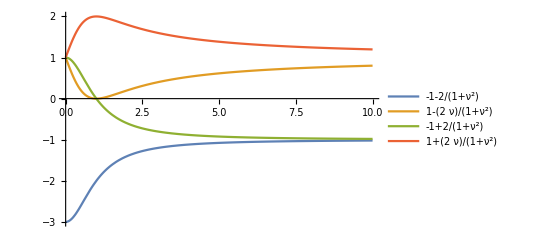

```mathematica
Plot[{-1-2/(1+ν^2),1-(2 ν)/(1+ν^2),-1+2/(1+ν^2),1+(2 ν)/(1+ν^2)},{ν,0,10},PlotLegends->"Expressions"]
```

With λ_1=1, λ_2=-(ⅈ (-ⅈ+ν))/(1+ν^2), λ_3=1, λ_4=(ⅈ (ⅈ+ν))/(1+ν^2)

```mathematica
Table[-2Sum[Re[-(ⅈ (-ⅈ+ν))/(1+ν^2)]Cos[(k(j-1)π)/(1+1)],{j,2,2}]-(-1)^k 1-2Sum[Im[-(ⅈ (-ⅈ+ν))/(1+ν^2)]Sin[(k(j-1)π)/(1+1)],{j,2,2}],{k,0,3}]//ComplexExpand
```

{-1+2/(1+ν^2),1+(2 ν)/(1+ν^2),-1-2/(1+ν^2),1-(2 ν)/(1+ν^2)}

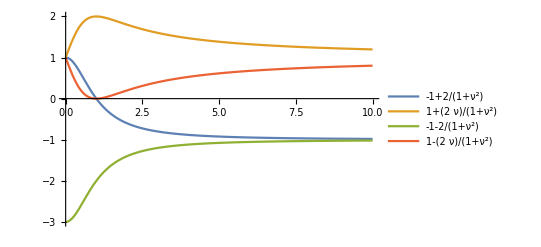

```mathematica
Plot[{-1+2/(1+ν^2),1+(2 ν)/(1+ν^2),-1-2/(1+ν^2),1-(2 ν)/(1+ν^2)},{ν,0,10},PlotLegends->"Expressions"]
```

### Hence the min max quantity is 1+(2 ν)/(1+ν^2)>1 for ν>0, but λ_1=1, so this is an impossible situation, λ_1≥ min max can never hold, when size=4.

For size=5

The exact condition

```mathematica
({{(16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4)}})[[1]]
```

{(16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4),(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4),(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4),(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4),(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}

```mathematica
Reduce[4-2 ν+ν^2≥0&&-8-4 ν^2+ν^3>0]
```

```mathematica
ν>Root[-8-4 #1^2+#1^3&,1]//N
```

ν>4.41114

The eigenvalues

```mathematica
({{(16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4)}, {(ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4), (ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4)}, {(ν (8+4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (ν^2 (4-2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν^2 (4+2 ν+ν^2))/(16+20 ν^2+5 ν^4), (ν (-8-4 ν^2+ν^3))/(16+20 ν^2+5 ν^4), (16+12 ν^2+ν^4)/(16+20 ν^2+5 ν^4)}})//Eigenvalues//ToRadicals
```

{1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4)}

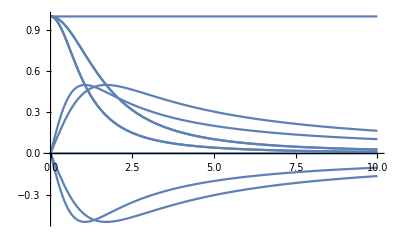

```mathematica
Plot[ReIm/@{1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4)},{ν,0,10}]
```

size=2m+1=5, so m=2. 
With different admissible permutations: pay attention to the conjugate-even property when arranging the eigenvalues!

Case 1

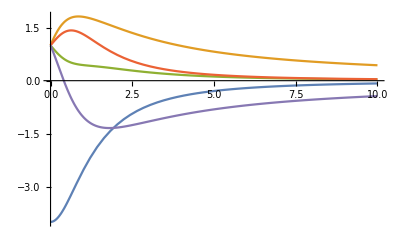

```mathematica
{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],Subscript[λ, 4],Subscript[λ, 5]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

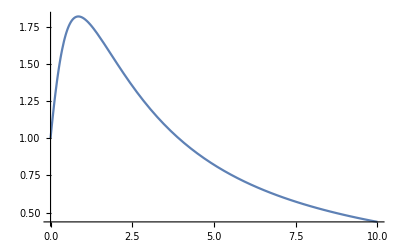

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,1,1}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,1,1}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Case 2

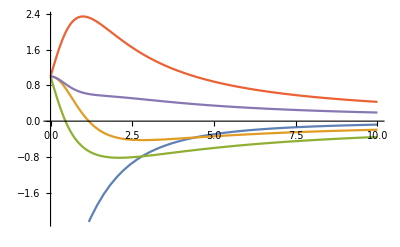

```mathematica
{Subscript[λ, 1],Subscript[λ, 5],Subscript[λ, 3],Subscript[λ, 4],Subscript[λ, 2]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

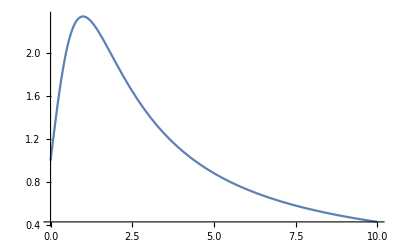

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,3,3}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,3,3}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+20 ν^2+10^(1/4) ν (√(5+√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5-√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Case 3

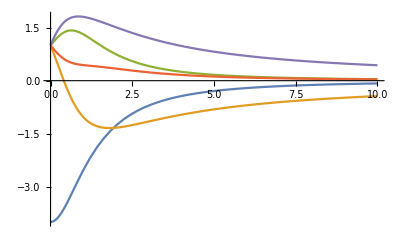

```mathematica
{Subscript[λ, 1],Subscript[λ, 5],Subscript[λ, 4],Subscript[λ, 3],Subscript[λ, 2]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,4,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

-Graphics-

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,4,4}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Case 4

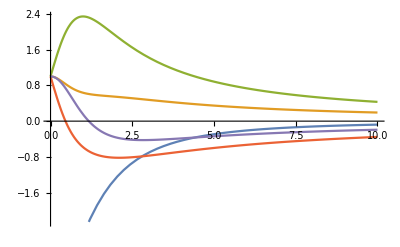

```mathematica
{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 4],Subscript[λ, 3],Subscript[λ, 5]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,2,2}]//ComplexExpand,ν>0],{ν,0,10}]
```

-Graphics-

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,2,2}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+20 ν^2+10^(1/4) ν (√(5+√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5-√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Case 5

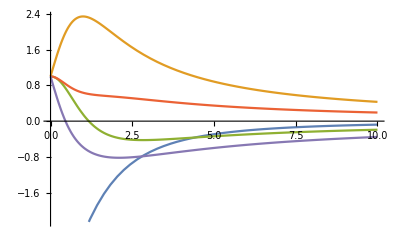

```mathematica
{Subscript[λ, 1],Subscript[λ, 3],Subscript[λ, 2],Subscript[λ, 5],Subscript[λ, 4]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,1,1}]//ComplexExpand,ν>0],{ν,0,10}]
```

-Graphics-

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,1,1}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+20 ν^2+10^(1/4) ν (√(5+√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5-√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Case 6

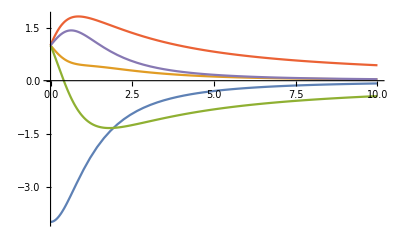

```mathematica
{Subscript[λ, 1],Subscript[λ, 3],Subscript[λ, 5],Subscript[λ, 2],Subscript[λ, 4]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,3,3}]//ComplexExpand,ν>0],{ν,0,10}]
```

-Graphics-

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,3,3}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Case 7

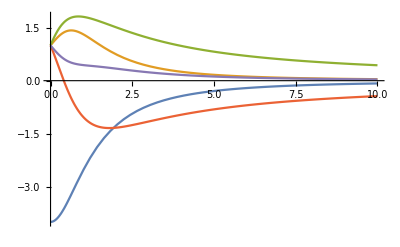

```mathematica
{Subscript[λ, 1],Subscript[λ, 4],Subscript[λ, 2],Subscript[λ, 5],Subscript[λ, 3]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,2,2}]//ComplexExpand,ν>0],{ν,0,10}]
```

-Graphics-

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,2,2}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Case 8

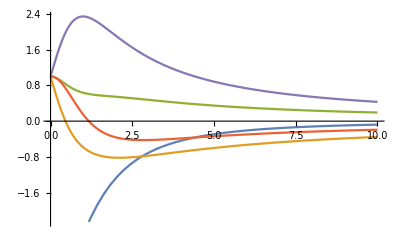

```mathematica
{Subscript[λ, 1],Subscript[λ, 4],Subscript[λ, 5],Subscript[λ, 2],Subscript[λ, 3]}={1,(16+10 ν^2+2 √5 ν^2-√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2-√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2-2 √5 ν^2+√10 √(-16 ν^2-(16 ν^2)/(√5)-16 ν^4-5 ν^6+√5 ν^6))/(16+20 ν^2+5 ν^4),(16+10 ν^2+2 √5 ν^2+√10 √(-16 ν^2+(16 ν^2)/(√5)-16 ν^4-5 ν^6-√5 ν^6))/(16+20 ν^2+5 ν^4)};Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,0,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

```mathematica
Plot[Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,4,4}]//ComplexExpand,ν>0],{ν,0,10}]
```

-Graphics-

```mathematica
Evaluate@Simplify[Table[-2Sum[Re[Subscript[λ, j]]Cos[(2k(j-1)π)/5],{j,2,3}]-2Sum[Im[Subscript[λ, j]]Sin[(2k(j-1)π)/5],{j,2,3}],{k,4,4}]//ComplexExpand,ν>0]
```

{1/(16+20 ν^2+5 ν^4)(16+20 ν^2+10^(1/4) ν (√(5+√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5-√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))}

Combining them to form the min-max: there are just 2 different functions

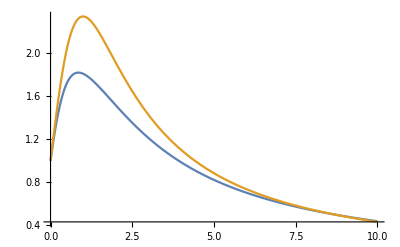

```mathematica
Plot[{1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4))),1/(16+20 ν^2+5 ν^4)(16+20 ν^2+10^(1/4) ν (√(5+√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5-√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))},{ν,0,10}]
```

The min crosses level 1:

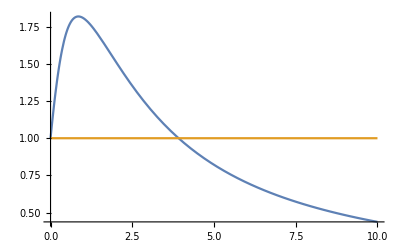

```mathematica
Plot[{1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4))),1},{ν,0,10}]
```

```mathematica
1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))==1//Solve
```

$Aborted

```mathematica
Reduce[1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))==1&&ν≥0,Reals]
```

$Aborted

```mathematica
NSolve[1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))==1&&ν≥0,Reals]
```

{{ν→0.},{ν→3.91732}}

```mathematica
FindRoot[1/(16+20 ν^2+5 ν^4)(16+10^(1/4) ν (√(5-√5) (256 (3+√5)+256 (5+√5) ν^2+960 ν^4-80 (-5+√5) ν^6-25 (-3+√5) ν^8)^(1/4)+√(5+√5) (-256 (-3+√5)-256 (-5+√5) ν^2+960 ν^4+80 (5+√5) ν^6+25 (3+√5) ν^8)^(1/4)))==1,{ν,4},WorkingPrecision->16]
```

{ν→3.917320537037615}

### Conclusion: for size=5, the general theory says ν>3.91 is necessary in order for the spectrum to be realizable by a non-negative circulant matrix. The exact value in our case is ν>4.41114. Reason: our circulant matrix has an even more specific structure.